## Análise dimensional

```mathematica
pr=2.206*10^7 
pw=1.177*10^7 
dp=0.005 
k=10^-13 
Dr=2000 
Dw=0.1  
Lw=400 
mu=0.005 
rho=800 
Remin=100
```

2.206×10^7 Pa

1.177×10^7 Pa

0.005 Pa

m^2/10000000000000

2000 m

0.1 m

400 m

0.005 (1 Pa).(1 s)

800 kg/m^3

100

## Variáveis comuns

```mathematica
pr=2.206*10^7;
pw=1.177*10^7;
dp=200000;
k=10^-13;
Dr=2000;
Dw=0.1;
Lw=400;
mu=0.005;
rho=800;
Remin=100;
Kvw=2*Pi*k/(mu*Log[Dr/Dw])(*vertical wellbore*)
V[x]:=4*Q[x]/(π*Dw^2)(*velocity, keep it here for now*)
Rey[x_]:=rho*V[x]*Dw/mu(*reynolds, keep it here for now*)
```

1.26888×10^-11

```mathematica
Rey[x]=rho*4*Q[x]/(π*Dw^2)*Dw/mu//Simplify
```

2.03718×10^6 Q[x]

## caso f linear (K=cte, vertical wellbore)

p'[x]==-2037.18 Q[x]

Q'[x]==0.000279916-1.26888×10^-11 p[x]

{{Q→InterpolatingFunction[…],p→InterpolatingFunction[…]}}

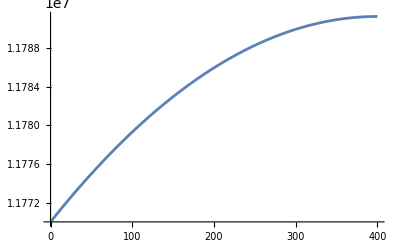

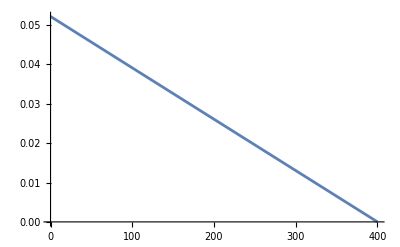

{1.179124269×10^7}

{1.177×10^7}

{-21242.7}

{0.05215536594}

```mathematica
flinear[Q_]:=16/((4 rho Q)/(Dw mu π))
eq1Linear=p'[x]==-32*flinear[Q[x]]*rho*Q[x]^2/(π^2 Dw^5)
eq2Linear=Q'[x]==-Kvw*(p[x]-pr)//Simplify 
res=NDSolve[{eq1Linear,eq2Linear,Q[0]==0.0,p[Lw]==pw},{Q,p},{x,0,Lw}]//Simplify//Chop 
(*res=DSolve[{eq1Linear,eq2Linear,Q[0]==0.0,p[Lw]==pw},{Q,p},{x}]//Simplify//Chop *)(*tentativa de gerar analitico*)
Plot[Evaluate[{p[Lw-x]}/.res[[1]]],{x,Lw,0},PlotRange->All]
Plot[Evaluate[{Q[Lw-x]}/.res[[1]]],{x,Lw,0},PlotRange->All]
NumberForm[Evaluate[{p[0]}/.res[[1]]],10]
NumberForm[Evaluate[{p[Lw]}/.res[[1]]],10]
DeltaP=Evaluate[{p[Lw]}/.res[[1]]]-Evaluate[{p[0]}/.res[[1]]]
NumberForm[Evaluate[{Q[Lw]}/.res[[1]]],10]
```

## caso f não linear (K=cte, vertical wellbore)

p'[x]==-543074. Q[x]^1.75

Q'[x]==0.000279916-1.26888×10^-11 p[x]

{{Q→InterpolatingFunction[…],p→InterpolatingFunction[…]}}

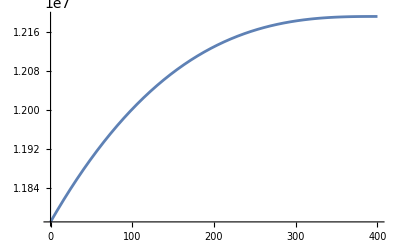

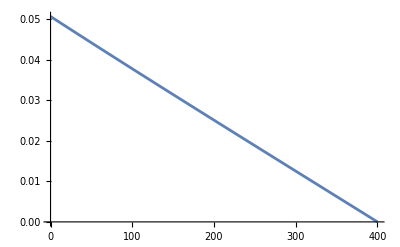

{1.219297411×10^7}

{1.176999979×10^7}

{-422974.}

{0.05065050899}

```mathematica
fnonlinear[Q_]:=0.0791/((4 rho Q)/(Dw mu π))^0.25
eq1NonLinear=p'[x]==-32*fnonlinear[Q[x]]*rho*Q[x]^2/(π^2 Dw^5)
eq2NonLinear=Q'[x]==-Kvw*(p[x]-pr)//Simplify 
res=NDSolve[{eq1NonLinear,eq2NonLinear,Q[0]==0.0,p[Lw]==pw},{Q,p},{x,0,Lw},Method->"Shooting", InitialSeeding->{p[0]==pw+dp}]//Simplify//Chop 
Plot[Evaluate[{p[Lw-x]}/.res[[1]]],{x,Lw,0},PlotRange->All]
Plot[Evaluate[{Q[Lw-x]}/.res[[1]]],{x,Lw,0},PlotRange->All]
NumberForm[Evaluate[{p[0]}/.res[[1]]],10]
NumberForm[Evaluate[{p[Lw]}/.res[[1]]],10]
DeltaP=Evaluate[{p[Lw]}/.res[[1]]]-Evaluate[{p[0]}/.res[[1]]]
NumberForm[Evaluate[{Q[Lw]}/.res[[1]]],10]
```

## caso f linear (K=linear)

p'[x]==-2037.18 Q[x]

Q'[x]==-3.17221×10^-14 x (-2.206×10^7+p[x])

NDSolve::precw: The precision of the differential equation ({{p'[x]==-2037.18 Q[x],Q'[x]==-3.17221×10^-14 x (-2.206×10^7+p[x]),Q[0]==0.,p[400]==1.177×10^7},{},{},{},{}}) is less than WorkingPrecision (35.).

{{Q→InterpolatingFunction[…],p→InterpolatingFunction[…]}}

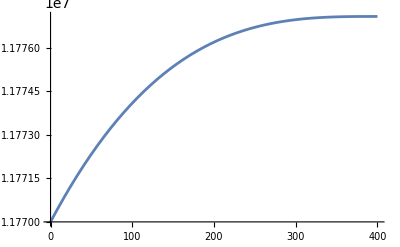

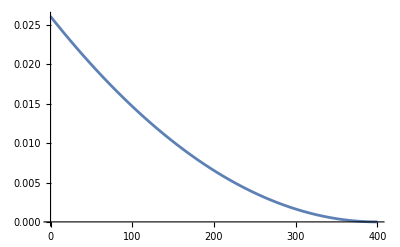

{1.177708919×10^7}

{1.177×10^7}

{-7089.19}

{0.02610282486}

```mathematica
flinear[Q_]:=16/((4 rho Q)/(Dw mu π))
K[x_]:=Kvw*x/Lw
eq1Linear=p'[x]==-32*flinear[Q[x]]*rho*Q[x]^2/(π^2 Dw^5)
eq2Linear=Q'[x]==-K[x]*(p[x]-pr)//Simplify 
res=NDSolve[{eq1Linear,eq2Linear,Q[0]==0.0,p[Lw]==pw},{Q,p},{x,0,Lw},AccuracyGoal->20,PrecisionGoal->20,WorkingPrecision->35]//Simplify//Chop 
(*res=DSolve[{eq1Linear,eq2Linear,Q[0]==0.0,p[Lw]==pw},{Q,p},{x}]//Simplify//Chop *)(*tentativa de gerar analitico*)
Plot[Evaluate[{p[Lw-x]}/.res[[1]]],{x,Lw,0},PlotRange->All]
Plot[Evaluate[{Q[Lw-x]}/.res[[1]]],{x,Lw,0},PlotRange->All]
NumberForm[Evaluate[{p[0]}/.res[[1]]],10]
NumberForm[Evaluate[{p[Lw]}/.res[[1]]],10]
DeltaP=Evaluate[{p[Lw]}/.res[[1]]]-Evaluate[{p[0]}/.res[[1]]]
NumberForm[Evaluate[{Q[Lw]}/.res[[1]]],10]
```

## caso f não linear (K linear)

p'[x]==-543074. Q[x]^1.75

Q'[x]==-3.17221×10^-14 x (-2.206×10^7+p[x])

FindRoot::trcx: The search has encountered a complex value and the trust region step control method is only implemented for real values.

NDSolve::berr: The scaled boundary value residual error of 612719. indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

{{Q→InterpolatingFunction[…],p→InterpolatingFunction[…]}}

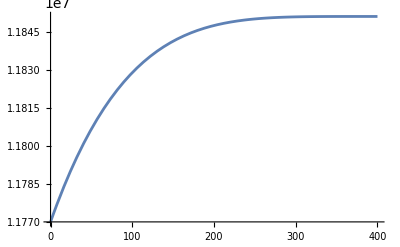

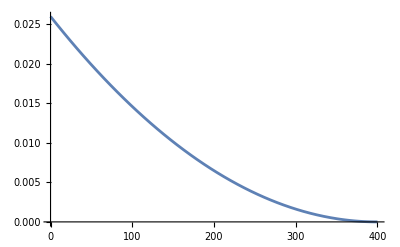

{1.185092996×10^7}

{1.176999273×10^7}

{-80937.2}

{0.02597138317}

```mathematica
fnonlinear[Q_]:=0.0791/((4 rho Q)/(Dw mu π))^0.25
K[x_]:=Kvw*x/Lw
eq1NonLinear=p'[x]==-32*fnonlinear[Q[x]]*rho*Q[x]^2/(π^2 Dw^5)
eq2NonLinear=Q'[x]==-K[x]*(p[x]-pr)//Simplify 
res=NDSolve[{eq1NonLinear,eq2NonLinear,Q[0]==0.0,p[Lw]==pw},{Q,p},{x,0,Lw},Method->"Shooting", InitialSeeding->{p[0]==pw+dp},PrecisionGoal->12]//Simplify//Chop 
Plot[Evaluate[{p[Lw-x]}/.res[[1]]],{x,Lw,0},PlotRange->All]
Plot[Evaluate[{Q[Lw-x]}/.res[[1]]],{x,Lw,0},PlotRange->All]
NumberForm[Evaluate[{p[0]}/.res[[1]]],10]
NumberForm[Evaluate[{p[Lw]}/.res[[1]]],10]
DeltaP=Evaluate[{p[Lw]}/.res[[1]]]-Evaluate[{p[0]}/.res[[1]]]
NumberForm[Evaluate[{Q[Lw]}/.res[[1]]],10]
```

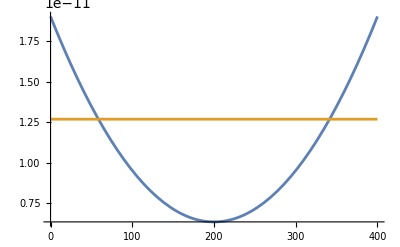

1.26888×10^-11

6.34442×10^-12

0.

```mathematica
(*testando*)
Kf[x_]:=4 Kvw x^2/Lw^2 - 4 Kvw x/Lw+3 Kvw/2
Plot[{Kf[x],Kvw},{x,0,Lw},PlotRange->All]
Kvw
Kf[Lw/2]
Kf[Lw]-Kf[0]
```

## caso f linear (K parabólico)

p'[x]==-2037.18 Q[x]

Q'[x]==(-1.90333×10^-11+1.26888×10^-13 x-3.17221×10^-16 x^2) (-2.206×10^7+p[x])

NDSolve::precw: The precision of the differential equation ({{p'[x]==-2037.18 Q[x],Q'[x]==(-1.90333×10^-11+1.26888×10^-13 x-3.17221×10^-16 x^2) (-2.206×10^7+p[x]),Q[0]==0.,p[400]==1.177×10^7},{},{},{},{}}) is less than WorkingPrecision (35.).

{{Q→InterpolatingFunction[…],p→InterpolatingFunction[…]}}

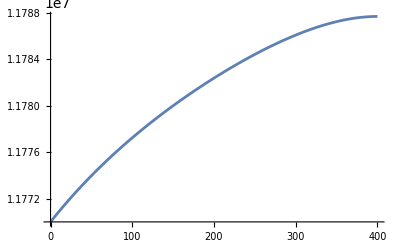

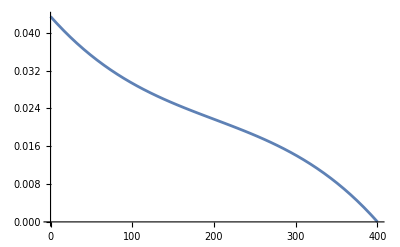

{1.178770713×10^7}

{1.177000000×10^7}

{-17707.1273458960653861045338059}

{0.04347630488}

```mathematica
flinear[Q_]:=16/((4 rho Q)/(Dw mu π))
K[x_]:=4 Kvw x^2/Lw^2 - 4 Kvw x/Lw+3 Kvw/2(*parabólico*)
eq1Linear=p'[x]==-32*flinear[Q[x]]*rho*Q[x]^2/(π^2 Dw^5)
eq2Linear=Q'[x]==-K[x]*(p[x]-pr)//Simplify 
res=NDSolve[{eq1Linear,eq2Linear,Q[0]==0.0,p[Lw]==pw},{Q,p},{x,0,Lw},AccuracyGoal->20,PrecisionGoal->20,WorkingPrecision->35]//Simplify//Chop 
(*res=DSolve[{eq1Linear,eq2Linear,Q[0]==0.0,p[Lw]==pw},{Q,p},{x}]//Simplify//Chop *)(*tentativa de gerar analitico*)
Plot[Evaluate[{p[Lw-x]}/.res[[1]]],{x,Lw,0},PlotRange->All]
Plot[Evaluate[{Q[Lw-x]}/.res[[1]]],{x,Lw,0},PlotRange->All]
NumberForm[Evaluate[{p[0]}/.res[[1]]],10]
NumberForm[Evaluate[{p[Lw]}/.res[[1]]],10]
DeltaP=Evaluate[{p[Lw]}/.res[[1]]]-Evaluate[{p[0]}/.res[[1]]]
NumberForm[Evaluate[{Q[Lw]}/.res[[1]]],10]
```

## caso f não linear (K parabólico)

p'[x]==-543074. Q[x]^1.75

Q'[x]==(-1.90333×10^-11+1.26888×10^-13 x-3.17221×10^-16 x^2) (-2.206×10^7+p[x])

{{Q→InterpolatingFunction[…],p→InterpolatingFunction[…]}}

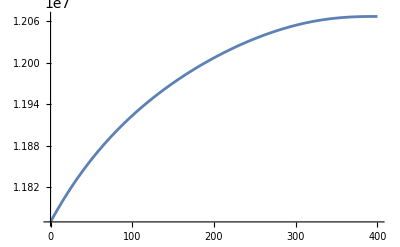

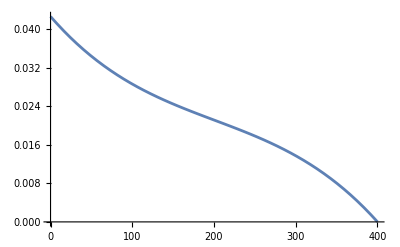

{1.206718661×10^7}

{1.177×10^7}

{-297187.}

{0.04267083913}

```mathematica
fnonlinear[Q_]:=0.0791/((4 rho Q)/(Dw mu π))^0.25
K[x_]:=4 Kvw x^2/Lw^2 - 4 Kvw x/Lw+3 Kvw/2(*parabólico*)
eq1NonLinear=p'[x]==-32*fnonlinear[Q[x]]*rho*Q[x]^2/(π^2 Dw^5)
eq2NonLinear=Q'[x]==-K[x]*(p[x]-pr)//Simplify 
res=NDSolve[{eq1NonLinear,eq2NonLinear,Q[0]==0.0,p[Lw]==pw},{Q,p},{x,0,Lw},Method->"Shooting", InitialSeeding->{p[0]==pw+dp},PrecisionGoal->13]//Simplify//Chop 
Plot[Evaluate[{p[Lw-x]}/.res[[1]]],{x,Lw,0},PlotRange->All]
Plot[Evaluate[{Q[Lw-x]}/.res[[1]]],{x,Lw,0},PlotRange->All]
NumberForm[Evaluate[{p[0]}/.res[[1]]],10]
NumberForm[Evaluate[{p[Lw]}/.res[[1]]],10]
DeltaP=Evaluate[{p[Lw]}/.res[[1]]]-Evaluate[{p[0]}/.res[[1]]]
NumberForm[Evaluate[{Q[Lw]}/.res[[1]]],10]
```

## caso f linear e f não linear juntos (não funcionando)

```mathematica
(*f[Q_]:=Piecewise[{{16/((4 rho Q)/(Dw mu π)),((4 rho Q)/(Dw mu π))<=1187.38},{0.0791/((4 rho Q)/(Dw mu π))^0.25,((4 rho Q)/(Dw mu π))>1187.38}}]//Simplify*)
flinear[Q_]:=16/((4 rho Q)/(Dw mu π))
fnonlinear[Q_]:=0.0791/((4 rho Q)/(Dw mu π))^0.25

f[Q_]:=flinear[Q]
eq1=p'[x]==-32*f[Q[x]]*rho*Q[x]^2/(π^2 Dw^5)
eq2=Q'[x]==-Kvw*(p[x]-pr)//Simplify 

res=NDSolve[{eq1,eq2,Q[0]==0.0,p[Lw]==pw},{Q,p},{x,0,Lw}]//Simplify//Chop (*funciona para o caso linear*)
(*res=NDSolve[{eq1,eq2,Q[0]==0.0,p[Lw]==pw},{Q,p},{x,0,Lw},Method->"Shooting", InitialSeeding->{p[0]==pw+dp}]//Simplify//Chop (*funciona para o caso não linear*)*)
(*res=NDSolve[{eq1,eq2,Q[0]==0.0,p[Lw]==pw,WhenEvent[Rey[x]<=1187.38,f[x]->16/Rey[x]],WhenEvent[Rey[x]>1187.38,f[x]->0.0791/Rey[x]^0.25]},{Q,p},{x,0,Lw},Method->"Shooting", InitialSeeding->{p[0]==pw+dp},DiscreteVariables->{f}]//Simplify//Chop*) (*TESTANDO*)

Plot[Evaluate[{p[Lw-x]}/.res[[1]]],{x,Lw,0},PlotRange->All]
Plot[Evaluate[{Q[Lw-x]}/.res[[1]]],{x,Lw,0},PlotRange->All]
Evaluate[{p[0]}/.res[[1]]]
Evaluate[{p[Lw]}/.res[[1]]]
DeltaP=Evaluate[{p[Lw]}/.res[[1]]]-Evaluate[{p[0]}/.res[[1]]]
Evaluate[{Q[Lw]}/.res[[1]]]
```